## Automated process for creating graphical representation with the Wigner-D functions

```mathematica
ClearAll["Global`*"]
```

### Author: Robert Poenaru Date: 25th August 🗓

### Constant spin for a system

```mathematica
spin=1;
```

Create a set of projections M and K,  for a given spin

```mathematica
wfComp[spin_]:=Table[{spin,m,k},{m,-spin,spin},{k,-spin,spin}];
```

Generate a set of Euler Angles using a pure function

```mathematica
angles[]={RandomReal[{π/6,π}],RandomReal[{π/6,π}],RandomReal[{π/6,π}]};
```

```mathematica
state0=wfComp[spin][[1]];
```

```mathematica
printer[state_]:=Do[Print["|IMK> = ","|",state[[i,1]]," ",state[[i,2]]," ",state[[i,3]]," >"],{i,1,2*spin+1}];
printer[state0]
```

|IMK> = |1 -1 -1 >

|IMK> = |1 -1 0 >

|IMK> = |1 -1 1 >

```mathematica
wigner[state_]:=Table[Re[WignerD[state[[i]],angles[][[1]],angles[][[2]],angles[][[3]]]],{i,1,2*spin+1}];
```

```mathematica
wigner[state0]
```

{0.153339,0.310139,0.135744}

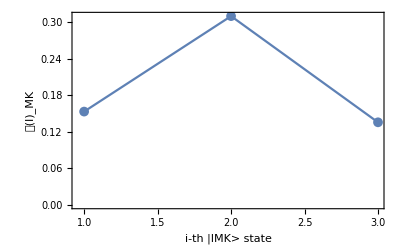

```mathematica
ListPlot[wigner[state0],PlotRange->Full,Axes->False,Frame->True,PlotMarkers->{Automatic, Medium},Joined->True,FrameLabel->{"i-th |IMK> state","𝒟(I)_MK"}]
```